```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/ece1228-electromagnetic-theory"]

fs=Style[#,FontSize->14]&;
```

/Users/pjoot/project/figures/ece1228-electromagnetic-theory

Plots of transmission magnitude and phase for a one dimensional photonic crystal.
Plots assume: μ_i = μ_i= 1, normal incidence, and use the Fresnel reflection coefficient ρ_ij for the TE mode polarization.

## ece1228 problem set 9, problem 2 (2016)

```mathematica
ClearAll[ mui, muj, ni, nj, rho, di, dj, c, g, ej, ej, a, b, acap, bcap, m, display, phii, phij]
mui = 1;
muj = 1;
ni = 1 ;
nj = 3.4 - 0.002 I ;
rho = (ni/mui - nj/muj)/(ni/mui + nj/muj);
di = 1.76 10^(-2) ;  (*meters*)
dj = 1.33 10^(-2) ;  (*meters*)
c = 2.998×10^8 ; (* meters/second*)
(*phi[omega] = -beta d = -(omega/c) n d cos(theta) ; theta = 0. *)
phii = -# ni di/c &;
phij = -# nj dj/c &;
g = 1/(1 - rho^2);
ei = Exp[I phii[#]] &;
ej = Exp[I phij[#]]&;
a = (ej[#] -rho^2/ej[#]) ei[#] &;
acap = ((1/ej[#]) - ej[#] rho^2)/ei[#] & ;
b = -rho(ej[#] - 1/ej[#])/ei[#] & ;
bcap = rho(ej[#] - 1/ej[#]) ei[#] &;
m = g {{a[#], b[#]}, {bcap[#], acap[#]}}&;
display = {psi -> ψ, omega ->ω,I -> j, -I -> -j };
(*(SetPrecision[m[ω],3] /. display)// MatrixForm *)

(*No need to explicitly calculate the eigensystem for the matrix.The MatrixPower function is doing that anyways.*)

ClearAll[out, psi]
(*psi = Subscript[E, r,N] at the Subscript[L, PC] point*)
psi = 1; (*set equal to one so that it doesn't have to be cancelled out.  Mathematica is deferring that simplification, and it messes up the plots, making them show zero since the plot expressions contain symbols. *)
out = {0,psi ei[#]} &;
(*out[omega] /. display // MatrixForm*)
```

```mathematica
ClearAll[x, r, t, ghz, pabs, parg, n, nn, omega1, omega2]
x[omega_, n_] := MatrixPower[m[omega],n]. out[omega]  // FullSimplify;

r[omega_, n_] := (x[omega,n][[1]])/(x[omega, n][[2]]) ;
t[omega_, n_] := psi/(x[omega, n][[2]]) ;
ghz = 10^9 ; (*1/sec*)

omega1 = 20 ghz;
omega2  = 23 ghz ;
pabs[nn_] :=Plot[Abs[t[omega ghz, nn]], {omega, omega1/ghz, omega2/ghz}, 
AxesLabel->{"ω (GHz)", "|T(ω)|"}, 
PlotStyle->Thick,
ImageSize -> 325];
parg[nn_]:=Plot[Arg[t[omega ghz,nn]] 180/Pi, {omega, omega1/ghz, omega2/ghz},
PlotStyle->Thick,
AxesLabel->{"ω (GHz)", "arg(T(ω))"}, 
ImageSize -> 325];
Manipulate[
Column[{pabs[n],parg[n]}],
{{n,3},1,20,1}]
```

```mathematica
p0 = DynamicModule[{n=3},Column[{pabs[n],parg[n]}]]
```

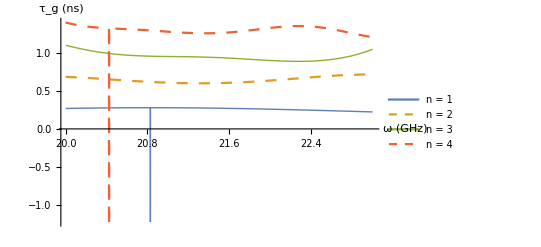

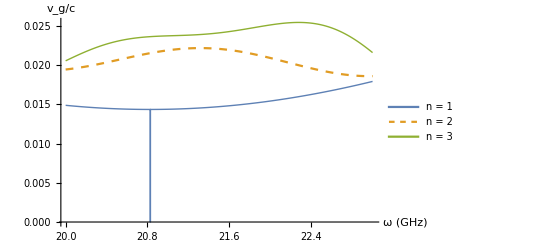

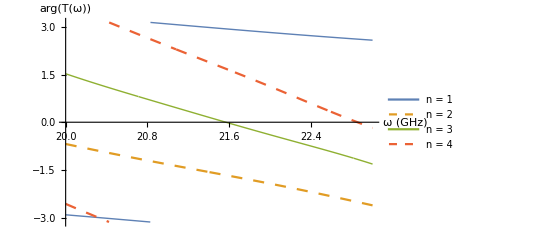

```mathematica
ClearAll[groupDelay, deltaOmega, secondsToNanoseconds, groupVelocity, dashes]
deltaOmega = 0.0005 ghz ;
secondsToNanoseconds = 10^9;
groupDelay[n_] := Module[{list,tauG},
list = Table[ Arg[t[omega,n]], {omega, omega1, omega2, deltaOmega}] ;
tauG = -(list // Differences)/deltaOmega;
{ (omega1 + deltaOmega * #)/ghz, secondsToNanoseconds tauG[[#]]} &/@ Range[Length[tauG]]
]

groupVelocity[tauG_, n_] := Module[{lPC},
lPC =(n-1)(di + dj) + dj ;
{tauG[[#]][[1]], c lPC/tauG[[#]][[2]]/secondsToNanoseconds} &/@ Range[Length[tauG]]
]

groupDelays = groupDelay[#] & /@ Range[4] ;

p1 = ListLinePlot[ groupDelays, AxesLabel->{ "ω (GHz)", "τ_g (ns)" }, PlotLegends->Placed[(StringForm["n = ``",#] &/@ Range[4] ),{Right, Bottom}], PlotStyle -> {Thick,(Dashing[#]&/@{0.002,0.008,0.014,0.02})}  ]
p2 = ListLinePlot[ groupVelocity[groupDelays[[#]],#] & /@ Range[3], AxesLabel->{ "ω (GHz)", "v_g/c" },  PlotLegends->Placed[(StringForm["n = ``",#] &/@ Range[3] ),{Right, Bottom}], PlotStyle -> {Thick,(Dashing[#]&/@{0.002,0.008,0.014})} ]
p3 = Plot[ Evaluate[Arg[t[omega ghz,#]] & /@ Range[4]] , {omega, omega1/ghz, omega2/ghz},AxesLabel->{"ω (GHz)", "arg(T(ω))"}, PlotLegends->Placed[(StringForm["n = ``",#] &/@ Range[4] ),{Right, Top}] , PlotStyle -> {Thick,(Dashing[#]&/@{0.002,0.008,0.014,0.02}) }]
```

```mathematica
peeters`exportForLatex["ps9PartaTransmissionFunctionFig1", p0]
peeters`exportForLatex["ps9PartbGroupDelayFig2", p1]
peeters`exportForLatex["ps9PartcGroupVelocityFig3", p2]
```

{ps9PartaTransmissionFunctionFig1.eps,ps9PartaTransmissionFunctionFig1pn.png}

{ps9PartbGroupDelayFig2.eps,ps9PartbGroupDelayFig2pn.png}

{ps9PartcGroupVelocityFig3.eps,ps9PartcGroupVelocityFig3pn.png}